# Brendan Philbin

## Simple Ising Model Equilibration Number of spins = 4 Number of iterations = 100

## β = 0.1

```mathematica
numSweeps=Range[0,100];
trial1={4,0,4,0,4,0,0,4,0,-12,0,0,-12,-12,0,4,0,-12,0,0,0,0,0,0,4,0,4,0,0,-12,-12,-12,0,4,0,-12,-12,-12,0,-12,-12,-12,-12,-12,0,4,0,0,-12,-12,-12,-12,-12,0,4,0,4,0,4,0,4,0,4,0,4,0,4,0,-12,-12,0,0,-12,-12,-12,0,0,4,0,-12,0,4,0,4,0,0,4,0,4,0,0,0,4,0,0,4,0,4,0,4,0};
trial1data=Transpose[{numSweeps,trial1}];
```

## β = 1

```mathematica
trial2={0,0,0,0,0,0,0,0,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12};
trial2data=Transpose[{numSweeps,trial2}];
```

## β = 10

```mathematica
trial3={0,0,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12,-12};
trial3data=Transpose[{numSweeps,trial3}];
```

## Energy Plots

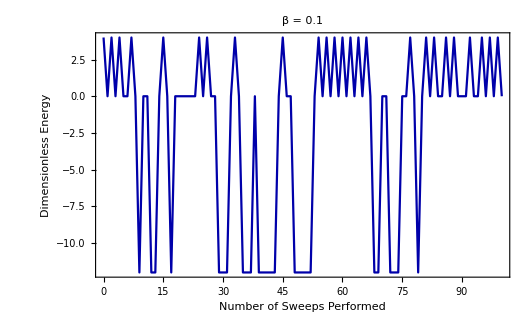

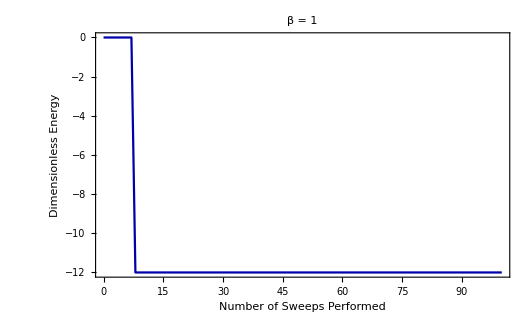

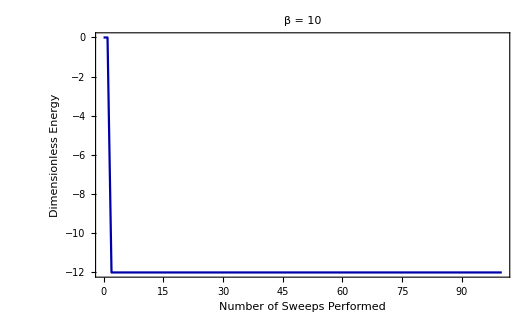

```mathematica
trial1plot=ListLinePlot[trial1data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"β = 0.1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
trial2plot=ListLinePlot[trial2data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"β = 1", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
trial3plot=ListLinePlot[trial3data,Frame->True,FrameLabel->{"Number of Sweeps Performed","Dimensionless Energy"},PlotLabel->"β = 10", PlotStyle->Darker[Blue],FrameStyle->Black,LabelStyle->Black]
```